Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

2 - 8 Double integrals
Describe the region of integration and evaluate.

3.  ∫_0^3 ∫_-y^y (x^2+y^2)ⅆxⅆy

```mathematica
ClearAll["Global`*"]
```

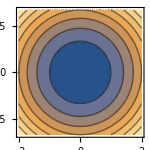

```mathematica
ContourPlot[{x^2+y^2},{x,-2,2},{y,-2,2},ImageSize->150]
```

This is a circle in 2d, in 3d a pothole.

```mathematica
e1=Integrate[Integrate[x^2+y^2,{x,-y,y}],{y,0,3}]
```

54

I don’t have the intermediate answer for the above, Mathematica just performed the double integration in one step.

5.  ∫_0^1 ∫_(x^2)^x (1-2x y)ⅆyⅆx

```mathematica
ClearAll["Global`*"]
```

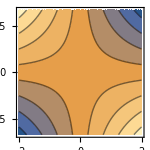

```mathematica
e1=ContourPlot[(1-2 x y),{x,-2,2},{y,-2,2},ImageSize->150]
```

This is a saddle surface.

```mathematica
e2=Integrate[Integrate[(1-2 x y),{y,x^2,x}],{x,0,1}]
```

1/12

6.  ∫_0^2 ∫_0^y Sinh[x+y]ⅆxⅆy

7.  ∫_2^0 ∫_y^0 Sinh[x+y]ⅆxⅆy(problem 6, order reversed)

```mathematica
ClearAll["Global`*"]
```

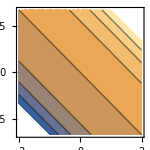

```mathematica
e1=ContourPlot[Sinh[x+y],{x,-2,2},{y,-2,2},ImageSize->150]
```

This is a beveled corner, but in 2d, can’t tell whether inside of corner is up or down.

```mathematica
e3=Integrate[Integrate[(Sinh[x+y]),{x,y,0}],{y,2,0}]//Simplify
```

(-1+Cosh[2]) Sinh[2]

```mathematica
e4=PossibleZeroQ[(-1+Cosh[2]) Sinh[2]-(1/2 Sinh[4]-Sinh[2])]
```

True

The answer above is equivalent to the text answer, as shown by the PZQ. I did not understand what was meant by ‘order reversed’, I thought it referred to the order of integration, not the order of integration limits.

9 - 11 Volume
Find the volume of the given region in space.

9. The region beneath z=4 x^2+9 y^2 and above the rectangle with vertices {0,0},{3,0},{3,2},{0,2}

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=ContourPlot3D[z==4 x^2+9 y^2,{x,-2,4},{y,-1.75,2.5}, {z,0,36},AxesLabel->{x,y,z},ImageSize->200];
```

```mathematica
e3=Graphics3D[Hexahedron[{{0,0,0},{3,0,0},{3,2,0},{0,2,0},{0,0,36},{3,0,36},{3,2,36},{0,2,36}}]];
```

```mathematica
Show[e1,e3]
```

-Graphics3D-

```mathematica
wib=Integrate[Integrate[4 x^2+9 y^2,{x,0,3}],{y,0,2}]
```

144

```mathematica
∫_0^2 ∫_0^3 (4 x^2+9 y^2)ⅆxⅆy
```

144

11. The region above the xy-plane and below the paraboloid z=1-(x^2+y^2).

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=ContourPlot3D[z==1-(x^2+y^2),{x,-2,2},{y,-2,2},{z,0,2},ImageSize->200]
```

-Graphics3D-

```mathematica
e2=Solve[(x^2+y^2)==1,x]
```

{{x→-√(1-y^2)},{x→√(1-y^2)}}

```mathematica
e3=Integrate[Integrate[1-(x^2+y^2),{x,-√(1-y^2),√(1-y^2)}],{y,-1,1}]
```

π/2

12 - 16 Center of gravity
Find the center of gravity {x̄, ȳ} of a mass of density f(x, y) = 1 in the given region R.

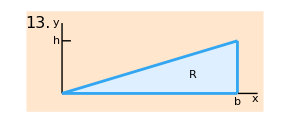

```mathematica
Graphics[{{LightOrange,Rectangle[{0,0},{4,1.7}]},{LightBlue,Polygon[{{0.6,0.31},{3.56,0.31},{3.56,1.2}}]},{Line[{{0.6,0.31},{0.6,1.5}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.007],Line[{{0.6,0.31},{3.56,0.31}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.007],Line[{{3.56,0.31},{3.56,1.2}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.007],Line[{{0.6,0.31},{3.56,1.2}}]},{Line[{{0.6,1.2},{0.75,1.2}}]},{Text[Style["h",Medium],{0.5,1.2}]},{Text[Style["y",Medium],{0.5,1.5}]},{Text[Style["b",Medium],{3.56,0.16}]},{Text[Style["x",Medium],{3.85,0.22}]},{Line[{{3.57,0.31},{3.9,0.31}}]},{Text[Style["R",Medium,Italic],{2.8,0.63}]},{Text[Style["13.",16],{0.2,1.5}]}},ImageSize->290]
```

```mathematica
ClearAll["Global`*"]
```

To find the total mass given the density, I need to integrate the function over the region. But I can’t just use the width and height, which would double the true result.

```mathematica
e1M=1/2 Integrate[Integrate[1,{x,0,b}],{y,0,h}]
```

(b h)/2

This problem is covered in s.m., where the method of deducing the y-function is discussed. What is explained is that the y-function needs to follow the hypoteneuse, so y=(h x)/b.

```mathematica
x̄=1/e1M Integrate[Integrate[x 1,{y,0,(h x)/b}],{x,0,b}]
```

(2 b)/3

This gives the x coordinate. For the y, it is the same setup, with the only difference being the y as the integrand of the inside integral.

```mathematica
ȳ=1/e1M Integrate[Integrate[y 1,{y,0,(h x)/b}],{x,0,b}]
```

h/3

Note: Mathematica version 10 has a function which calculates the answer automatically. It is called RegionCentroid. (See problem 15).

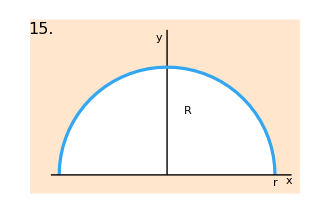

```mathematica
Graphics[{{LightOrange,Rectangle[{0,0},{6.5,4.2}]},{White,Disk[{3.3,0.45},2.6,{0,π}]},{Line[{{3.3,0.45},{3.3,3.95}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.007],Circle[{3.3,0.45},2.6,{0,π}]},{Text[Style["y",Medium],{3.1,3.75}]},{Text[Style["r",Medium],{5.9,0.26}]},{Text[Style["x",Medium],{6.25,0.3}]},{Line[{{0.5,0.45},{6.3,0.45}}]},{Text[Style["R",Medium,Italic],{3.8,2}]},{Text[Style["15.",16],{0.25,3.95}]}},ImageSize->330]
```

```mathematica
disk=Disk[{0,0},r,{0,π}]
```

Disk[{0,0},r,{0,π}]

```mathematica
RegionCentroid[disk]
```

{0,(4 r)/(3 π)}

17 - 20 Moments of inertia
Find I_x, I_y, I_0 of a mass of density f[x,y] = 1 in the region R in the figures, which the engineer is likely to need, along with other profiles listed in engineering handbooks.

17. R as in problem 13.

The second moment of inertia can be calculated from axes through the centroid, but with a triangle it should be an easy matter. I used the formula for moments of inertia on text p. 429.

```mathematica
ℛ=ImplicitRegion[0≤x≤b&&0≤y≤h&&y≤h/b x,{x,y}];
```

First to calculate I_x as

```mathematica
Integrate[y^2,{x,y}∈ℛ]
```

Piecewise[{{0, (b>0&&h==0)||!(h≥0&&b>0)}, {(b h^3)/12, True}}]

Then to calculate I_y as

```mathematica
Integrate[x^2,{x,y}∈ℛ]
```

Piecewise[{{b^3/3, b>0&&h==0}, {(b^3 h)/4, b>0&&h>0}, {0, True}}]

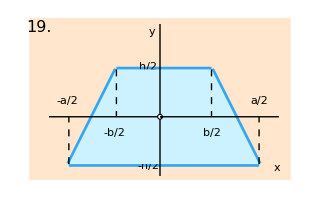

```mathematica
Graphics[{{LightOrange,Rectangle[{0,0},{6.6,4.1}]},{RGBColor[0.2,0.65,0.95],Thickness[0.012],Line[{{1,0.4},{5.8,0.4}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.012],Line[{{2.2,2.8},{4.6,2.8}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.012],Line[{{1,0.4},{2.2,2.8}}]},{RGBColor[0.2,0.65,0.95],Thickness[0.012],Line[{{4.6,2.8},{5.8,0.4}}]},{RGBColor[0.8,0.95,1],Polygon[{{1,0.4},{5.8,0.4},{4.6,2.8},{2.2,2.8},{1,0.4}}]},{Line[{{3.3,0.1},{3.3,3.95}}]},{Text[Style["y",Medium],{3.1,3.75}]},{Text[Style["a/2",Medium],{5.8,2}]},{Text[Style["x",Medium],{6.25,0.3}]},{Line[{{0.5,1.6},{6.3,1.6}}]},{Dashed,Line[{{1,0.4},{1,1.6}}]},{Dashed,Line[{{5.8,0.4},{5.8,1.6}}]},{Dashed,Line[{{4.6,2.8},{4.6,1.6}}]},{Dashed,Line[{{2.2,2.8},{2.2,1.6}}]},{EdgeForm[{Black}],FaceForm[White],Disk[{3.3,1.6},0.06,{0,2π}]},{Text[Style["-a/2",Medium],{0.95,2}]},{Text[Style["-b/2",Medium],{2.15,1.2}]},{Text[Style["b/2",Medium],{4.6,1.2}]},{Text[Style["19.",16],{0.25,3.85}]},{Text[Style["h/2",Medium],{3,2.85}]},{Text[Style["-h/2",Medium],{3,0.36}]}},ImageSize->320]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(b/2)/(a/2)
```

b/a

The figure is a regular trapazoid (isosceles). I intended to calculate the right side and then double it. So I went about it as

```mathematica
ℛ=ImplicitRegion[-h/2≤y≤h/2&&0≤x&&y≤-b/a x,{x,y}];
```

```mathematica
Integrate[y^2,{x,y}∈ℛ,Assumptions->{a,b,h}>0]
```

Piecewise[{{0, (a<0&&b<0&&h==0)||(a>0&&b>0&&h==0)||(a<0&&b==0&&h==0)||(a<0&&b>0&&h==0)||(a>0&&b<0&&h==0)||(a>0&&b==0&&h==0)||!((h≥0&&a>0)||(h≥0&&a<0))}, {(a h^4)/(64 b), (a<0&&b<0&&h>0)||(a>0&&b>0&&h>0)}, {∞ Sign[h]^3, (a<0&&b==0&&h>0)||(a>0&&b==0&&h>0)}, {-(5 a h^4)/(192 b)+∞ Sign[h]^3, True}}]

Above: useless. Consider the following grid for I_x

```mathematica
Grid[{{"I_x (1)","I_x (2)","I_x (3)"},{(h^3(3a+b))/12,(h^3(a^2+4a b+b^2))/(36(a+b)),((a+b)h^3)/24}},Frame->All]
```

I_x (1) | I_x (2) | I_x (3)
1/12 (3 a+b) h^3 | ((a^2+4 a b+b^2) h^3)/(36 (a+b)) | 1/24 (a+b) h^3

Or the grid for I_y

```mathematica
Grid[{{"I_y (1)","I_y (2)","I_y (3)"},{(h(a+b)(a^2+7 b^2))/48,(h^3(a+b)(a^2+b^2))/48,(h(a^4-b^4))/(48(a-b))}},Frame->All]
```

I_y (1) | I_y (2) | I_y (3)
1/48 (a+b) (a^2+7 b^2) h | 1/48 (a+b) (a^2+b^2) h^3 | ((a^4-b^4) h)/(48 (a-b))

No agreement seen in these.
Sources for the above. @(1) is https://www.efunda.com/math/areas/IsosTrapezoid.cfm (looks like isosceles case)
@(2) is https://structx.com/Shape_Formulas_015.html (the page is for isosceles)
@(3) is the text answer for this problem.

Note: In MMA version 10.4 a new function was introduced called MomentOfInertia. I don’t have 10.4 but I have 11.1. I tried it out but it don’t return an answer.

To me MomentOfInertia is not very impressive. It appears unable to process a point of rotation given in symbolic form.

```mathematica
RegionCentroid[ImplicitRegion[-h/2≤y≤h/2&&0≤x&&y≤-b/a x,{x,y}]]
```

ConditionalExpression[Piecewise[{{{0,0}, (a<0&&b<0&&h==0)||(a>0&&b>0&&h==0)}, {{(a h)/(6 b),-h/3}, (a<0&&b<0&&h>0)||(a>0&&b>0&&h>0)}, {{Indeterminate,Indeterminate}, (a<0&&b==0&&h>0)||(a>0&&b==0&&h>0)}, {{∞/(-(3 a h^2)/(8 b)+h ∞),(a h^3)/(24 b (-(3 a h^2)/(8 b)+h ∞))}, True}}],(a>0&&b>0&&h≥0)||(a>0&&h>0)||(a<0&&b<0&&h≥0)||(a<0&&h>0)]

```mathematica
isotrap=Polygon[{{-a/2,-h/2},{a/2,-h/2},{b/2,h/2},{-b/2,h/2}}]
```

Polygon[{{-a/2,-h/2},{a/2,-h/2},{b/2,h/2},{-b/2,h/2}}]

The following seems like a pretty large defect in the program, in that this function also seem incapable of operating on symbol variables.

```mathematica
RegionCentroid[isotrap]
```

RegionCentroid::nmet: Unable to compute the centroid of region Polygon[{{-a/2,-h/2},{a/2,-h/2},{b/2,h/2},{-b/2,h/2}}].

RegionCentroid[Polygon[{{-a/2,-h/2},{a/2,-h/2},{b/2,h/2},{-b/2,h/2}}]]

```mathematica
isotrapp=Polygon[{{-3,-1.5},{3,-1.5},{2,1.5},{-2,1.5}}]
```

Polygon[{{-3,-1.5},{3,-1.5},{2,1.5},{-2,1.5}}]

The defect seems confirmed when specific values are used. By the way, as seen here, it is not necessary to draw the last side of the polygon when looking for its centroid, it is merely required to get all the points listed.

```mathematica
RegionCentroid[isotrapp]
```

{0.,-0.1}

```mathematica
d2=ImplicitRegion[-1.5≤y≤1.5&&y≤-(1.5 x)/3&&y≤(1.5 x)/3,{x,y}]
```

ImplicitRegion[-1.5≤y≤1.5&&y≤-0.5 x&&y≤0.5 x,{x,y}]

An explicitly described implicit region can also be processed.

```mathematica
RegionCentroid[d2]
```

{-8.40257×10^-19,-1.}